```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
data=Import["Results/dldw_a1nm_v0.5_b2.5nm_extF2.dat"];
```

```mathematica
data[[3]]/.{a_,b_,c_,d_,e_,f_,g_,h_,i_,j_,k_,l_,m_}->{a,k}
```

{w(au),dpHedwx}

```mathematica
dLEedwx=data[[4;;]]/.{a_,b_,c_,d_,e_,f_,g_,h_,i_,j_,k_,l_,m_}->{a,j};
dLHedwx=data[[4;;]]/.{a_,b_,c_,d_,e_,f_,g_,h_,i_,j_,k_,l_,m_}->{a,k};
```

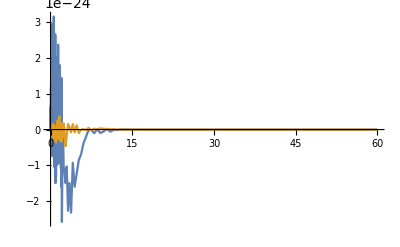

```mathematica
ListPlot[{dLEedwx,dLHedwx}, PlotRange->All, Joined->True]
```

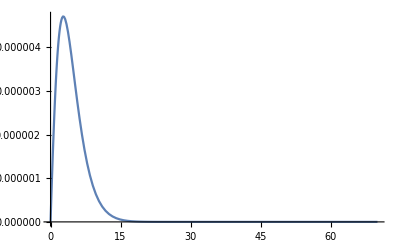

```mathematica
ListPlot[dLHedwx, PlotRange->All, Joined->True]
```

```mathematica
dLHedwx[[700]]
```

{67.5571,0}

```mathematica
dataP=Import["dpdw_a1nm_v0.5_b1.5nm.dat"];
```

```mathematica
dataP[[1]]
```

{w(au),dpEdwx,dpHdwx,dpEdwz,dpHdwz,dpEsdwx,dpHsdwx,dpEsdwz,dpHsdwz,dpEedwx,dpHedwx,dpEedwz,dpHedwz}

```mathematica
dPEedwx=dataP[[2;;]]/.{a_,b_,c_,d_,e_,f_,g_,h_,i_,j_,k_,l_,m_}->{a,j};
dPHedwx=dataP[[2;;]]/.{a_,b_,c_,d_,e_,f_,g_,h_,i_,j_,k_,l_,m_}->{a,k};
```

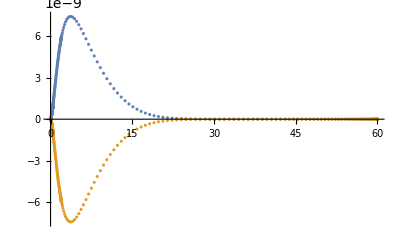

```mathematica
ListPlot[{dPEedwx,dPHedwx}, PlotRange->All]
```